```mathematica
F[k_,η1_,η2_]:=π/4*Re[HankelH1[1.4,k*η1]*HankelH2[7/5,k*η2]]
```

```mathematica
ρ[k_,η1_,η2_]:=-π/2*Im[HankelH1[1.4,k*η1]*HankelH2[7/5,k*η2]]
```

```mathematica
P[k_,α_]:=1/(2*π^2)*η^3*k^3*(F[k,η,η]-4*α*F[k,η,η0]*ρ[k,η,η0]+4*α^2*F[k,η0,η0]*ρ[k,η,η0]*ρ[k,η,η0])
```

```mathematica
η0:=1
```

```mathematica
η:=0.000001
```

```mathematica
NumericP1[l_?NumericQ]:=Log[P[Exp[l],0.1]]
```

```mathematica
NumericP2[l_?NumericQ]:=Log[P[Exp[l],1]]
```

```mathematica
kTicks={{Log[0.001],"0.001"},{Log[0.01],"0.01"}, {Log[0.1],"0.1"}, {Log[1],"1"}, {Log[10],"10"}, {Log[100],"10^2"}, {Log[1000],"10^3"}, {Log[10000],"10^4"}};
```

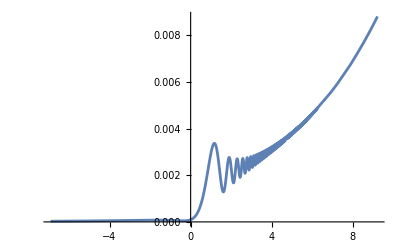

```mathematica
Plot[P[Exp[l],1],{l,Log[0.001],Log[10^4+1]}]
```

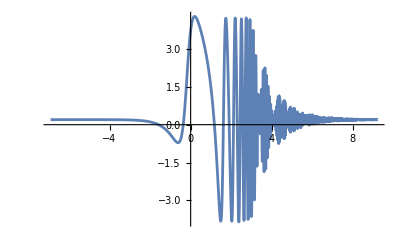

```mathematica
Plot[NumericP2'[l],{l,Log[0.001],Log[10^4+1]},PlotRange->All,EvaluationMonitor:>None]
```

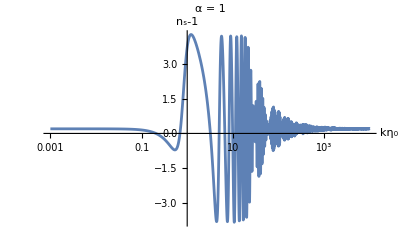

```mathematica
Show[%10, ScalingFunctions->{"Log",None},Ticks->{kTicks,Automatic},PlotRange->All,AxesLabel->{Style["kη_0",Italic,16],Style["n_s-1",16]},PlotLabel->Style["α = 1",16]]
```

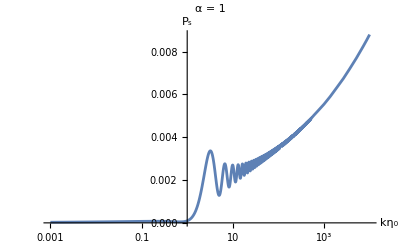

```mathematica
Show[%9, ScalingFunctions->{"Log",None},Ticks->{kTicks,Automatic},PlotRange->All,AxesLabel->{Style["kη_0",Italic,16],Style["P_s",16]},PlotLabel->Style["α = 1",16]]
```